Last modified on: Tuesday, July 10, 2018 at 19:23

Author Info

Lauren Berk

Carl Woll

MIT

Poster Session Content

Clustering and Visualizing EIWL Submissions

To create a function analogous to “Classify” that takes in a programming problem and student solutions (some correct, some incorrect) and builds a classifier that can determine if a given program is correct or incorrect, and more specifically, why the solution is correct or incorrect.  (If correct, which approach was taken.  If incorrect, what was done in error or misunderstood?)  We will develop this function using data from EIWL problems and  Wolfram Challenges.

Add the most representative image of your project here. (We recommend just 1 image, if you add more, we will make a collage of the images.)

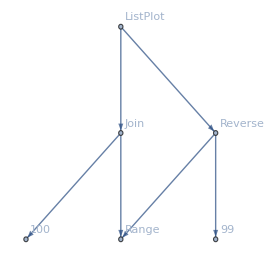
-Graphics--Graphics-

We created a function that takes in student solutions to arbitrary EIWL problems, collects the key components of the solutions, and clusters the solutions in order to understand common approaches to solving (or failing to solve) each problem.  We performed a truncated principal component analysis on the results so we could visualize the locations of these clusters in the space of symbol use.

We intend to go much deeper into analyzing this data, and data from the Wolfram Challenges.  We will explore the graph representation of code to generate additional distance metrics for clustering, look at performance of users over time and over problems, and generate automated helpful suggestions.

Note: Everything above this bar is your poster.Make sure it fits on a single page. "Preview Poster"

End of School Presentation Content

In addition to the poster content, include other content to present at the 2 minute presentation for end of school. Use the buttons below to add more sections."Add Header""Add Text""Add Code or Image"

Viewing principal components of student code submissions

Each element of this list represents a principal component or a “Direction”, or “strategy” that students employed in their code.

{{"List","Range"},{"List"},{"100","99"},{"ListPlot"},{"Join"},{"1"}}

Here each row represents how the different symbols contribute to each component.

-Graphics-

Then each cluster can be considered as a combination of these “strategies”.  Below, there is one row per cluster, and the values reflect their use of the six principal components (“strategies”).  From this you can see that Cluster (row) 3 is much more likely to use strategy 6 (include “1” in their code).  You can also see that Clusters 3 and 4 did not use strategy 4 (ListPlot).

-Graphics-

Exploring principal components of student code submissions

plotPCs[myresults, probList]

Note: Everything above this bar is in your 2 minute presentation. Make sure it fits on 2 slides. "Preview Presentation"

Detailed Project Notes

### Data file creation

#### import

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"Data"}];
```

#### Splitting the EIWL data file

```mathematica
eiwlData;
```

This is a list of associations.  Each element of eiwlData represents a single student-attempt and contains keys:

```mathematica
eiwlData[[3]] // Keys
```

{Timestamp,Exercise,CorrectQ,UserSubmission,AnswerKey,Text,Referer}

We want to save these problems in separate files for easy use and access.  To do this, we form a list of problem names

```mathematica
problemnames = eiwlData[[All,"Exercise"]] // Union;
```

We create a function that, given an exercise name, exports the subset of eiwlData containing solutions to those problems.  We can drop AnswerKey, Text, Referrer, and User.

```mathematica
eiwlDataImportantFields = KeyDrop[eiwlData,{"Timestamp","AnswerKey","Text", "User","Referer"}];
```

```mathematica
eiwlDataImportantFields = Dataset[eiwlDataImportantFields];
```

```mathematica
saveproblem[probname_] := Module[
{filename},
probdata = eiwlDataImportantFields[Select[#Exercise==probname&]];
filename = FileNameJoin[{NotebookDirectory[],"Data",StringJoin[StringReplace[probname,"."->"_"], ".mx"]}];
DumpSave[filename,probdata];
]
```

```mathematica
saveproblem /@ problemnames
```

### Data import

```mathematica
dataDir=FileNameJoin[{NotebookDirectory[],"Data"}];
```

```mathematica
allFiles = FileNames[___,dataDir];
```

```mathematica
Get["/Users/laurenberk/Dropbox (MIT)/Code Seal/CodeSeal_Summer/Sandbox/lauren/Data/3_6.mx"];
```

### Bag of words

#### pull submissions with good syntax

```mathematica
submittedCells=Normal@probdata[All,"UserSubmission"];
```

```mathematica
justCellData=submittedCells/.Cell[a_,___]:>Cell[a];
```

```mathematica
expressions=MakeExpression[justCellData,StandardForm];
```

```mathematica
goodSyntax=Select[expressions,FreeQ[ErrorBox]];
```

```mathematica
goodSyntax
```

{HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings],1}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,x],{x,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,21}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[Take[this is about strings,n],{n,1,21}]]],HoldComplete[Column[Table[Take[this is about strings,n],{n,1,Length[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],836,HoldComplete[Column[Sort[LetterNumber[thisisaboutstrings]]]],HoldComplete[Column[Sort[LetterNumber[this is about strings]]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[tihs is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n] {n,StringLength[tihs is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,21}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,21}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,21}]]],HoldComplete[Table[StringTake[this is about strings,n],{n,21}]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,Length[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]],HoldComplete[Column[Table[StringTake[this is about strings,n],{n,1,StringLength[this is about strings]}]]]}
 |  |  |  |

#### get bag of words

```mathematica
fillBags[expr_]:=Level[expr,{-1},Heads->True]/.ExpressionCell|HoldComplete|CompoundExpression | Null->Nothing
```

```mathematica
fillBags@goodSyntax[[1]];
```

```mathematica
bags=Map[ToString,fillBags/@goodSyntax,{2}];
```

```mathematica
bags[[1;;10]];
```

#### spelunking bags

```mathematica
ReverseSort@Counts@Flatten@Join@bags;
```

looking at the end result of clustering without thought, we need something to make better clusters, we will drop uncommon symbols

keep anything that shows up in >5% of the submissions

we need to know how many bags each word shows up in

```mathematica
allWords=Union@Flatten@bags;
```

```mathematica
howManyBagsAreYouIn=AssociationMap[Count[bags,{___,#,___},{1}]&,allWords];
```

```mathematica
keepers=Keys@Select[howManyBagsAreYouIn,#>0.01Length@goodSyntax&];
```

```mathematica
keepers
```

{0,1,20,21,Characters,Column,Function,i,Length,LetterNumber,List,n,Range,s,Set,Slot,Sort,str,StringJoin,StringLength,StringTake,Table,Take,TextWords,this is about string,this is about strings,this is about Strings,This is about strings,Times,x}

```mathematica
cleanBags=Replace[bags,word_/;Not@MemberQ[keepers,word]->Nothing,{2}];
```

```mathematica
cleanBags[[1]]
```

{Column,Table,StringTake,this is about strings,n,List,n,StringLength,this is about strings}

#### clustering bags

```mathematica
clusters=ClusterClassify[cleanBags]
```

ClassifierFunction[…]

```mathematica
groups=Map[#->clusters@#&,cleanBags];
```

```mathematica
grouped=GroupBy[groups,Last][[All,All,1]];
```

```mathematica
representatives=Map[Take[ReverseSort@Counts@grouped[#],UpTo@3]&,Keys@grouped];
```

```mathematica
Union[Flatten@#]&/@grouped // Normal // Column;
```

```mathematica
bags // Flatten // Counts  // Sort // Reverse;
```

### Creating a function wrapper

#### take in student submissions, output a classifier function

```mathematica
fillBags[expr_]:=Level[expr,{-1},Heads->True]/.ExpressionCell|HoldComplete|CompoundExpression |ErrorBox |  Null|"["|"]"|","|" "|RowBox->Nothing;

submissionsToBags[submissions_] := Module[
{submittedCells, justCellData, expressions, bags},

submittedCells=Normal@submissions[All,"UserSubmission"];
justCellData=submittedCells/.Cell[a_,___]:>Cell[a];
expressions=MakeExpression[justCellData,StandardForm];
bags=Map[ToString,fillBags/@expressions,{2}];
bags
]

classifyThese[classifier_, commonWords_][submissions_] := Module[
{submittedCells,justCellData,  expressions, bags, cleanBags, clusterNums},

bags=submissionsToBags[submissions];
cleanBags=Replace[bags,word_/;Not@MemberQ[commonWords,word]->Nothing,{2}];
clusterNums = classifier /@ cleanBags;
{bags,cleanBags, clusterNums}
]
```

```mathematica
codeClassiferBuilder[submissions_] :=Module[
{submittedCells, justCellData, expressions, goodSyntax, bags, words, howManyBagsAreYouIn, commonWords, cleanBags, myClassifier},

bags=submissionsToBags[submissions];
goodSyntax=Select[bags,FreeQ[ErrorBox]]; 

words =  Union@Flatten@goodSyntax;
howManyBagsAreYouIn=AssociationMap[Count[bags,{___,#,___},{1}]&,words];
commonWords=Keys@Select[howManyBagsAreYouIn,#>0.03Length@goodSyntax&];
cleanBags=Replace[bags,word_/;Not@MemberQ[commonWords,word]->Nothing,{2}];

myClassifier = ClusterClassify[cleanBags];
classifyThese[myClassifier, commonWords]
]
```

#### example of how this is used

```mathematica
myclassifier = codeClassiferBuilder[probdata];
```

```mathematica
{bags, cleanBags, clusterNums} = myclassifier[probdata];
```

```mathematica
groupMap=Map[cleanBags[[#]]->clusterNums[[#]]&,Range[Length[clusterNums]]];
```

```mathematica
grouped=GroupBy[groupMap,Last][[All,All,1]];
```

```mathematica
Union[Flatten@#]&/@grouped // Normal // Column
```

3→{0,0.2,1,Graphics3D,h,Hue,ImageCollage,List,n,Sphere,Style,Table}
4→{0,0.2,1,Graphics,Graphics3D,h,Hue,ImageCollage,List,n,Sphere,Style,Table,x}
2→{0,0.2,1,Graphics3D,Hue,ImageCollage,List,Sphere,Style,Table,x}
1→{0,0.2,1,Graphics3D,h,Hue,ImageCollage,List,Sphere,Style,Table}

```mathematica
(Union[Flatten@#]&/@grouped )[[3]] // InputForm
```

{"0", "0.2", "1", "Graphics3D", "Hue", "ImageCollage", "List", "Sphere", "Style", 
 "Table", "x"}

```mathematica
bags // Flatten // Counts  // Sort // Reverse
```

<|List→459,0→362,Hue→362,ImageCollage→362,Sphere→361,1→357,Table→356,0.2→355,Graphics3D→348,Style→317,n→267,h→225,x→138,4→20,Graphics→18,hue→15,
→13,c→10,t→8,r→6,Disk→6,{→6,k→6,}→5,9→4,RandomColor→4,Times→3,m→2,color→2,0.1→2,f→2,1.→2,p→2,Range→2,Slot→2,Function→2,Map→2,v→2,.2→2,Image→2,200→1,False→1,Boxed→1,Rule→1,0.8→1,0.6→1,0.4→1,0.→1,Grahics3D→1,DGraphics→1,3→1,  →1|>

### Getting cluster centers

#### Identifying cluster centers - starting with binaries

This association can actually be a first cut at cluster centers

```mathematica
centers = Union[Flatten@#]&/@grouped // Normal
```

{2→{1,100,99,Join,List,ListPlot,Range,Reverse,Times},1→{1,100,Join,ListPlot,Range,Reverse,Times},6→{1,100,99,Join,List,ListLinePlot,ListPlot,Plot,Range,Reverse,Times},4→{100,Join,Plot,Range,Reverse,Times},5→{100,99,Join,List,Plot,Range,Reverse},3→{1,100,ListPlot,Range,Reverse,Times},{}→{}}

We want to convert these lists to vectors / counts (and later move them to actual means over the sets and not binaries.  But for now -)

```mathematica
keywords = centers // Values // Flatten // Union
```

{1,100,99,Join,List,ListLinePlot,ListPlot,Plot,Range,Reverse,Times}

We want to map a list of words to a vector, indexed by the list of keywords, that indicates whether each keyword is contained in the list.  i.e. toVector[{a,b,c},{a,f,e,d,c}] = {1, 0, 1}

```mathematica
ContainsAny[{"1","100","99","Join","List","ListPlot","Range","Reverse","Times"},{#}]& /@ keywords
```

{True,True,True,True,True,False,True,False,True,True,True}

Now want to map this again

```mathematica
binaries = Outer[ContainsAny[#1,{#2}]&,(centers // Values),keywords,1]
```

{{True,True,True,True,True,False,True,False,True,True,True},{True,True,False,True,False,False,True,False,True,True,True},{True,True,True,True,True,True,True,True,True,True,True},{False,True,False,True,False,False,False,True,True,True,True},{False,True,True,True,True,False,False,True,True,True,False},{True,True,False,False,False,False,True,False,True,True,True},{False,False,False,False,False,False,False,False,False,False,False}}

We need to compute a covariance matrix, take the eigenvectors, and truncate them to approximate sparse principal component analysis

```mathematica
(cov = Dot[Transpose[mat],mat]/6//N )// MatrixForm
space = Eigenvectors[cov,3] // N  // MatrixForm
```

(-0.282286 | -0.395479 | -0.219169 | -0.339497 | -0.219169 | -0.08439 | -0.282286 | -0.197583 | -0.395479 | -0.395479 | -0.337532
-0.408269 | -0.00517424 | 0.358819 | 0.247821 | 0.358819 | 0.0844307 | -0.408269 | 0.487526 | -0.00517424 | -0.00517424 | -0.320663
0.31878 | -0.211909 | 0.484483 | -0.140641 | 0.484483 | 0.254805 | 0.31878 | -0.275883 | -0.211909 | -0.211909 | -0.178267)

```mathematica
Chop[space,.1]
```

(-0.282286 | -0.395479 | -0.219169 | -0.339497 | -0.219169 | 0 | -0.282286 | -0.197583 | -0.395479 | -0.395479 | -0.337532
-0.408269 | 0 | 0.358819 | 0.247821 | 0.358819 | 0 | -0.408269 | 0.487526 | 0 | 0 | -0.320663
0.31878 | -0.211909 | 0.484483 | -0.140641 | 0.484483 | 0.254805 | 0.31878 | -0.275883 | -0.211909 | -0.211909 | -0.178267)

#### Looking at fractions not binaries

```mathematica
centers = (Counts[Flatten@#]/ Length[#] //N)&/@grouped ;
keywords = centers // Values // Flatten // Union;
```

```mathematica
(centers // Values )[[1]][#]& /@ keywords
```

```mathematica
(allCenters = (Outer[#1[#2]&,(centers // Values),keywords,1] /. Missing[___]-> 0 ))// MatrixForm
```

(0.00822368 | 0.983553 | 0.987664 | 0.949013 | 0.015625 | 0 | 1.00164 | 0 | 1.98931 | 0.995066 | 0.00986842
0.00890963 | 1.98133 | 0 | 1.00297 | 0 | 0 | 1.00509 | 0 | 1.99194 | 0.996606 | 0.0093339
0.534622 | 1.56361 | 0.175523 | 0.605475 | 2.61889 | 0.105743 | 0.659689 | 0.0493827 | 1.68492 | 0.836286 | 0.0198604
0 | 1.97829 | 0 | 1. | 0 | 0 | 0 | 0.0723589 | 1.99276 | 0.998553 | 0.00434153
0 | 0.991471 | 0.991471 | 0.959488 | 0.0277186 | 0 | 0 | 0.0788913 | 1.96588 | 0.989339 | 0
0.017284 | 1.98025 | 0 | 0 | 0 | 0 | 1.02469 | 0 | 1.98025 | 1. | 0.0962963
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
(cov = Dot[Transpose[allCenters],allCenters]/6//N )// MatrixForm;
space = Eigenvectors[cov,3] // N  // MatrixForm;
Chop[space,.3]
```

(0 | -0.549768 | 0 | 0 | 0 | 0 | 0 | 0 | -0.661273 | -0.331353 | 0
0 | 0 | 0 | 0 | -0.956227 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.516565 | -0.683797 | -0.398033 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### Plotting cluster centers

#### Collecting the problem data

```mathematica
probList = {"3_6","5_6","10_10"};
```

```mathematica
fileList = Pick[allFiles,StringContainsQ[allFiles,Apply[Alternatives, probList]]];
```

```mathematica
Get /@ fileList;
```

```mathematica
problems = {};
For[i=1,i≤Length[probList],i++,
file = Pick[allFiles,StringContainsQ[allFiles,StringJoin["/",probList[[i]],"."]]][[1]];
Get[file];
AppendTo[problems, probdata];
]
```

#### Build all the classifiers

```mathematica
myclassifiers = codeClassiferBuilder /@problems;
```

```mathematica
Range[Length[probList]]
```

{1,2,3}

```mathematica
myresults = myclassifiers[[#]][problems[[#]]]& /@ Range[Length[probList]];
```

```mathematica
findPCs[probData_] := Module[
{groupMap, grouped, numGroups, centers, keywords, allCenters, cov, evectors, loadings, labels, tuples, tupleMap},
groupMap=Map[probData[[2]][[#]]->probData[[3]][[#]]&,Range[Length[probData[[2]]]]];
grouped=GroupBy[groupMap,Last][[All,All,1]];
grouped = Drop[grouped,{Length[grouped]}] ;

numGroups = Length[grouped];
maxPCindex = 6;

centers = (Counts[Flatten@#]/ Length[#] //N)&/@grouped ;
keywords = centers // Values  // Normal // Flatten // Keys // Union;
allCenters = (Outer[#1[#2]&,(centers // Values),keywords,1] /. Missing[___]-> 0 );
cov = Dot[Transpose[allCenters],allCenters]/(numGroups-1)//N;
evectors = Eigenvectors[cov,maxPCindex] // N;
evectors = Chop[evectors// N,Min[Max[Abs[#]]& /@ evectors]*.8]; (*Truncated eigenvectors - later replace with good SPCA method*)
evectors = (# / Norm[#])& /@ evectors; (*Normalizing*)
loadings = Outer[Dot[#1,#2]&,allCenters, evectors,1];

labels = Pick[keywords,#,b_ /;Abs[b]>0]& /@ evectors;

tuples = Subsets[Range[Length[evectors]],{3}];
tupleMap = Thread[tuples-> (tuples /. Thread[Union@Flatten@tuples-> labels])];
{tupleMap, loadings , labels, evectors}

]
```

```mathematica
plotPCs[multiProblems_, probList_] := Module[
{plotData},

plotData = findPCs[#]& /@ multiProblems;

Manipulate[
ListPointPlot3D [plotData[[probnum, 2]][[All,pcToShow ]]-> Range[Length[plotData[[probnum, 2]]]],
LabelingFunction->Callout,
AxesLabel-> Part[plotData[[probnum, 3]],pcToShow ]],
{{pcToShow,{1,2,3}},plotData[[probnum, 1]],ControlType-> PopupMenu},
{{probnum,1},Thread[Range[Length[multiProblems]]-> probList]},
SaveDefinitions -> True]

]
```

### Data Sources Links/References

Thanks to Stephen Wolfram and Richard Hennigan for  supplying us with this data set, and to Carl Woll and Kyle Keane for their help with this project!

### Keywords

Principal Component Analysis

Bag of Words

Educational Analytics